# 变换

先看看相关的基础函数

```mathematica
a={x,y,z};
√Dot[a,a]
Abs[a]
Norm[a]
Norm[a]//FullSimplify
EuclideanDistance[{0,0,0},a]
```

√(x^2+y^2+z^2)

{Abs[x],Abs[y],Abs[z]}

√(Abs[x]^2+Abs[y]^2+Abs[z]^2)

√(Abs[x]^2+Abs[y]^2+Abs[z]^2)

√(Abs[x]^2+Abs[y]^2+Abs[z]^2)

### 绘制直线根据函数变换的结果

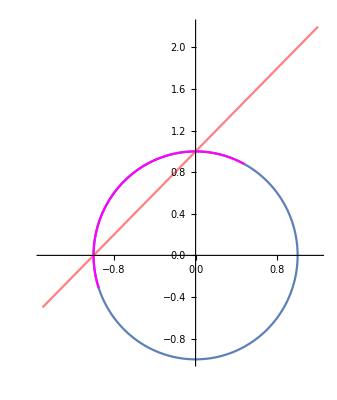

```mathematica
plot[f_,r_:{-1.5,1.2}]:=Block[{c,l},
c=ParametricPlot[{Cos[t],Sin[t]},{t,0,2π}];

l=ParametricPlot[{{t,t+1},{f[{t,t+1}]}},
(*Join[{t},r]*)(*{t,Sequence@@r}*)(*必须使用Evaluate*)
Evaluate@{t,Splice@r},PlotStyle->{Pink,Magenta}];
Show[c,l,PlotRange->1.2]]

plot[Normalize]
```

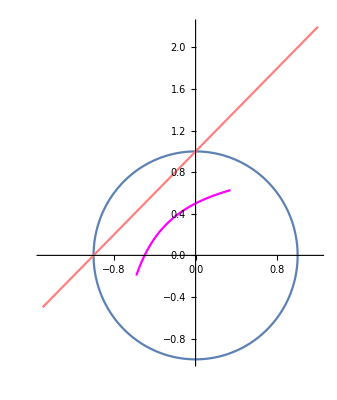

```mathematica
plot[#/(1+Norm[#])&]
```

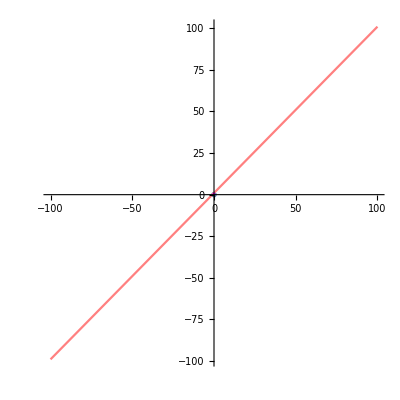

```mathematica
plot[#/(1+Norm[#])&,{-100,100}]
```

### 明白了以上变换过程后，我们看看3D空间中的曲面

```mathematica
ParametricPlot3D[{x,y,x y+1},{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[Normalize @{x,y,x y+1},{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[#/(1+Norm[#])& @{x,y,x y},{x,-50,50},{y,-50,50},PlotRange->All,PlotPoints->100]
```

-Graphics3D-

```mathematica
ParametricPlot3D[#/(1+Norm[#])&@{100x,100y,10^4 x y+1},{x,-1,1},{y,-1,1},PlotRange->1.2,PlotPoints->100]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[u],Sin[u],v},{u,0,2π},{v,-1,1}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[Normalize @{Cos[u],Sin[u],v},{u,0,2π},{v,-1,1}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[#/(1+Norm[#])& @{Cos[u],Sin[u],v},{u,0,2π},{v,-1,1}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[#/(1+Norm[#])& @{Cos[u],Sin[u],v},{u,0,2π},{v,-10,10},PlotRange->All,PlotPoints->33]
```

-Graphics3D-

```mathematica
(*{Abs@Cos[u]Cos[u],Abs@Sin[u]Sin[u],v}*)
ParametricPlot3D[{Sign@Cos[u] Cos[u]^2,Sign@Sin[u] Sin[u]^2,v},{u,0,2π},{v,-1,1},PlotRange->All,PlotPoints->33]
```

-Graphics3D-

```mathematica
ParametricPlot3D[Normalize@{Abs@Cos[u]Cos[u],Abs@Sin[u]Sin[u],v},{u,0,2π},{v,-1,1},PlotRange->All,PlotPoints->33]
```

-Graphics3D-

```mathematica
ParametricPlot3D[#1/(1+Norm[#1])&@{Sin[3u]Cos[u],Sin[3u]Sin[u],v},{u,0,π},{v,-10,10},PlotRange->All,PlotPoints->33]
```

-Graphics3D-

```mathematica
ParametricPlot3D[#1/(1+Norm[#1])&@{(Sin[3u]+2)Cos[u],(Sin[3u]+2)Sin[u],v},{u,0,2π},{v,-10,10},PlotRange->All,PlotPoints->33]
```

-Graphics3D-

```mathematica
ParametricPlot3D[Normalize@{(Sin[5u]+2)Cos[u],(Sin[5u]+2)Sin[u],v},{u,0,2π},{v,-10,10},PlotRange->All,PlotPoints->33]
```

-Graphics3D-

```mathematica
(Sin^2)[1.]
```

Sin^2[1.]